```mathematica
f[x_] = (3x + π)/(√(1+ x^2 + √((1+x^2)^3)))
```

(π+3 x)/(√(1+x^2+√((1+x^2)^3)))

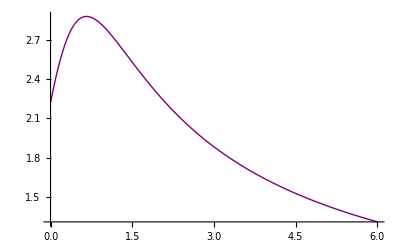

```mathematica
a = 0;
b = 6;
n1 = 6;
n2 = 10;
x0=2.4316;
h1=(b-a)/n1;
h2=(b-a)/n2;
graphic = Plot[f[x], {x, a, b},  PlotStyle ->{Purple, Thick}]
```

```mathematica
data1=Table[{i h1,f[i h1]},{i,0,n1}]//N
data2=Table[{i h2,f[i h2]},{i,0,n2}]//N
{TableForm[data1],TableForm[data2]}
```

{{0.,2.22144},{1.,2.79498},{2.,2.27263},{3.,1.88196},{4.,1.62248},{5.,1.44065},{6.,1.30598}}

{{0.,2.22144},{0.6,2.87905},{1.2,2.69633},{1.8,2.37169},{2.4,2.09635},{3.,1.88196},{3.6,1.71455},{4.2,1.58116},{4.8,1.47253},{5.4,1.38227},{6.,1.30598}}

{0. | 2.22144
1. | 2.79498
2. | 2.27263
3. | 1.88196
4. | 1.62248
5. | 1.44065
6. | 1.30598,0. | 2.22144
0.6 | 2.87905
1.2 | 2.69633
1.8 | 2.37169
2.4 | 2.09635
3. | 1.88196
3.6 | 1.71455
4.2 | 1.58116
4.8 | 1.47253
5.4 | 1.38227
6. | 1.30598}

```mathematica
(* А *)
Pl1[x_]=∏_(i=0)^n1 (x-data1[[i+1,1]])
Pl2[x_]=∏_(i=0)^n2 (x-data2[[i+1,1]])
```

(-6.+x) (-5.+x) (-4.+x) (-3.+x) (-2.+x) (-1.+x) (0.+x)

(-6.+x) (-5.4+x) (-4.8+x) (-4.2+x) (-3.6+x) (-3.+x) (-2.4+x) (-1.8+x) (-1.2+x) (-0.6+x) (0.+x)

```mathematica
LPl1[x_]=Sum[data1[[i+1,2]] Pl1[x]/((x-data1[[i+1,1]]) Pl1'[data1[[i+1,1]]]),{i,0,n1}]//Simplify
```

2.22144+2.25583 x-2.63235 x^2+1.19771 x^3-0.278813 x^4+0.0326847 x^5-0.0015262 x^6

```mathematica
LPl2[x_]=Sum[data2[[i+1,2]] Pl2[x]/((x-data2[[i+1,1]]) Pl2'[data2[[i+1,1]]]),{i,0,n2}]//Simplify
```

2.22144+2.49199 x-3.06027 x^2+1.2842 x^3+0.00622875 x^4-0.240723 x^5+0.114705 x^6-0.0277141 x^7+0.00384248 x^8-0.000291019 x^9+9.36214×10^-6 x^10

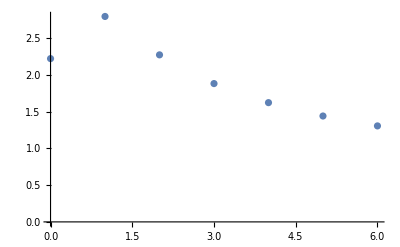

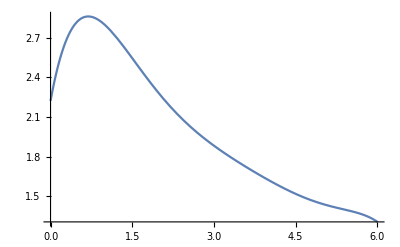

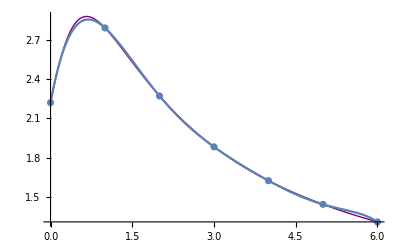

```mathematica
graph1 = ListPlot[data1]
graph1ln = Plot[LPl1[x], {x, a,b}]
Show[graphic, graph1, graph1ln]
```

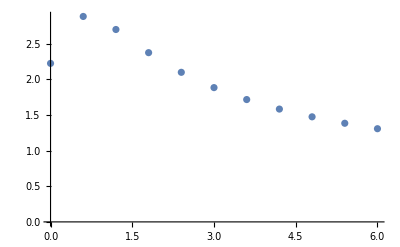

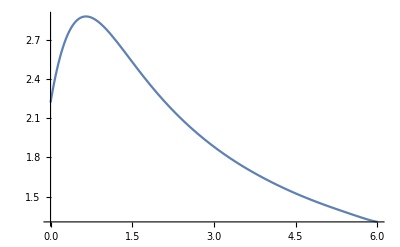

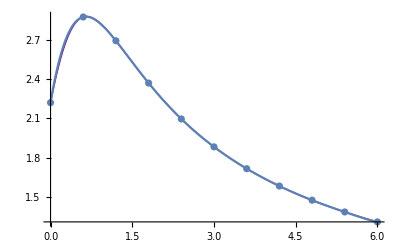

```mathematica
graph2 = ListPlot[data2]
graph2ln = Plot[LPl2[x], {x, a,b}]
Show[graphic, graph2, graph2ln]
```

```mathematica
tab1=Array[dif1,{n1+1,n1+1},{0,0}]
For[j=1,j≤n1,j++,
		For[i=n1,i≥n1-j,i--,dif1[i,j]=""]
	]
For[i=0,i≤n1,i++,dif1[i,0]=data1[[i+1,2]]]
For[j=1,j≤n1,j++,For[i=0,i≤n1-j,i++,dif1[i,j]=dif1[i+1,j-1]-dif1[i,j-1]]]
PaddedForm[TableForm[tab1],{n1,n1-1}]
```

2.22144 |  0.57354 | -1.09589 |  1.22757 | -1.22806 |  1.17500 | -1.09887
 2.79498 | -0.52235 |  0.13168 | -0.00049 | -0.05306 |  0.07613 | -
 2.27263 | -0.39067 |  0.13119 | -0.05355 |  0.02307 | - | -
 1.88196 | -0.25947 |  0.07764 | -0.03048 | - | - | -
 1.62248 | -0.18183 |  0.04716 | - | - | - | -
 1.44065 | -0.13467 | - | - | - | - | -
 1.30598 | - | - | - | - | - | -

```mathematica
{{" 2.22144", " 0.57354", "-1.09589", " 1.22757", "-1.22806", " 1.17500", "-1.09887"}, {" 2.79498", "-0.52235", " 0.13168", "-0.00049", "-0.05306", " 0.07613", ""}, {" 2.27263", "-0.39067", " 0.13119", "-0.05355", " 0.02307", "", ""}, {" 1.88196", "-0.25947", " 0.07764", "-0.03048", "", "", ""}, {" 1.62248", "-0.18183", " 0.04716", "", "", "", ""}, {" 1.44065", "-0.13467", "", "", "", "", ""}, {" 1.30598", "", "", "", "", "", ""}}
```

```mathematica
{{" 2.22144", " 0.57354", "-1.09589", " 1.22757", "-1.22806", " 1.17500", ""}, {" 2.79498", "-0.52235", " 0.13168", "-0.00049", "-0.05306", "", ""}, {" 2.27263", "-0.39067", " 0.13119", "-0.05355", "", "", ""}, {" 1.88196", "-0.25947", " 0.07764", "", "", "", ""}, {" 1.62248", "-0.18183", "", "", "", "", ""}, {" 1.44065", "", "", "", "", "", ""}, {" 1.30598", "", "", "", "", "", ""}}
```

```mathematica
tab2=Array[dif2,{n2+1,n2+1},{0,0}]
For[j=1,j≤n2,j++,
		For[i=n2,i≥n2-j,i--,dif2[i,j]=""]
	]
For[i=0,i≤n2,i++,dif2[i,0]=data2[[i+1,2]]]
For[j=1,j≤n2,j++,For[i=0,i≤n2-j,i++,dif2[i,j]=dif2[i+1,j-1]-dif2[i,j-1]]]
PaddedForm[TableForm[tab2],{n2,n2-1}]
```

{{dif2[0,0],dif2[0,1],dif2[0,2],dif2[0,3],dif2[0,4],dif2[0,5],dif2[0,6],dif2[0,7],dif2[0,8],dif2[0,9],dif2[0,10]},{dif2[1,0],dif2[1,1],dif2[1,2],dif2[1,3],dif2[1,4],dif2[1,5],dif2[1,6],dif2[1,7],dif2[1,8],dif2[1,9],dif2[1,10]},{dif2[2,0],dif2[2,1],dif2[2,2],dif2[2,3],dif2[2,4],dif2[2,5],dif2[2,6],dif2[2,7],dif2[2,8],dif2[2,9],dif2[2,10]},{dif2[3,0],dif2[3,1],dif2[3,2],dif2[3,3],dif2[3,4],dif2[3,5],dif2[3,6],dif2[3,7],dif2[3,8],dif2[3,9],dif2[3,10]},{dif2[4,0],dif2[4,1],dif2[4,2],dif2[4,3],dif2[4,4],dif2[4,5],dif2[4,6],dif2[4,7],dif2[4,8],dif2[4,9],dif2[4,10]},{dif2[5,0],dif2[5,1],dif2[5,2],dif2[5,3],dif2[5,4],dif2[5,5],dif2[5,6],dif2[5,7],dif2[5,8],dif2[5,9],dif2[5,10]},{dif2[6,0],dif2[6,1],dif2[6,2],dif2[6,3],dif2[6,4],dif2[6,5],dif2[6,6],dif2[6,7],dif2[6,8],dif2[6,9],dif2[6,10]},{dif2[7,0],dif2[7,1],dif2[7,2],dif2[7,3],dif2[7,4],dif2[7,5],dif2[7,6],dif2[7,7],dif2[7,8],dif2[7,9],dif2[7,10]},{dif2[8,0],dif2[8,1],dif2[8,2],dif2[8,3],dif2[8,4],dif2[8,5],dif2[8,6],dif2[8,7],dif2[8,8],dif2[8,9],dif2[8,10]},{dif2[9,0],dif2[9,1],dif2[9,2],dif2[9,3],dif2[9,4],dif2[9,5],dif2[9,6],dif2[9,7],dif2[9,8],dif2[9,9],dif2[9,10]},{dif2[10,0],dif2[10,1],dif2[10,2],dif2[10,3],dif2[10,4],dif2[10,5],dif2[10,6],dif2[10,7],dif2[10,8],dif2[10,9],dif2[10,10]}}

```mathematica
{{" 2.221441469", " 0.657608332", "-0.840323441", " 0.698390149", "-0.507149402", " 0.327555693", "-0.173587776", " 0.046271037", " 0.057055325", "-0.139847599", " 0.205423761"}, {" 2.879049801", "-0.182715109", "-0.141933291", " 0.191240748", "-0.179593709", " 0.153967917", "-0.127316739", " 0.103326361", "-0.082792275", " 0.065576162", ""}, {" 2.696334692", "-0.324648400", " 0.049307456", " 0.011647039", "-0.025625792", " 0.026651178", "-0.023990378", " 0.020534086", "-0.017216113", "", ""}, {" 2.371686291", "-0.275340944", " 0.060954495", "-0.013978754", " 0.001025385", " 0.002660800", "-0.003456291", " 0.003317973", "", "", ""}, {" 2.096345347", "-0.214386449", " 0.046975741", "-0.012953368", " 0.003686185", "-0.000795492", "-0.000138318", "", "", "", ""}, {" 1.881958898", "-0.167410708", " 0.034022373", "-0.009267184", " 0.002890693", "-0.000933810", "", "", "", "", ""}, {" 1.714548191", "-0.133388335", " 0.024755189", "-0.006376490", " 0.001956883", "", "", "", "", "", ""}, {" 1.581159856", "-0.108633145", " 0.018378699", "-0.004419607", "", "", "", "", "", "", ""}, {" 1.472526711", "-0.090254447", " 0.013959091", "", "", "", "", "", "", "", ""}, {" 1.382272264", "-0.076295355", "", "", "", "", "", "", "", "", ""}, {" 1.305976909", ", "", "", "", "", "", "", "", "", ""}}
```

```mathematica
T1=(x-b)/h1;
Pn1[x_]=dif1[n1,0];
P1[t_]=1;
```

```mathematica
For[k=1,k≤n1,k++,P1[t_]=P1[T1]*(T1+k-1);Pn1[x_]=Pn1[x]+dif1[n1-k,k]/(k!) P1[T1]]
Pn1[x]//Simplify
```

2.22144+2.25583 x-2.63235 x^2+1.19771 x^3-0.278813 x^4+0.0326847 x^5-0.0015262 x^6

```mathematica
T2=(x-b)/h2;
Pn2[x_]=dif2[n2,0];
P2[t_]=1;
For[k=1,k≤n2,k++,P2[t_]=P2[T2]*(T2+k-1);Pn2[x_]=Pn2[x]+dif2[n2-k,k]/(k!) P2[T2]]
Pn2[x]//Simplify
```

2.22144+2.49199 x-3.06027 x^2+1.2842 x^3+0.00622875 x^4-0.240723 x^5+0.114705 x^6-0.0277141 x^7+0.00384248 x^8-0.000291019 x^9+9.36214×10^-6 x^10

```mathematica
2.221441469079183+2.491989646126394 x-3.060274837665517 x^2+1.2842004327815701 x^3+0.006228748776026442 x^4-0.24072264816945838 x^5+0.1147053779535862 x^6-0.027714104136263042 x^7+0.0038424799158738453 x^8-0.00029101891640365097 x^9+9.362140195409848*^-6 x^10
```

```mathematica
graph1Pn=Plot[Pn1[x],{x,a,b}]
Show[graphic,graph1,graph1Pn]
```

-Graphics-

-Graphics-

```mathematica
graph2Pn=Plot[Pn2[x],{x,a,b}]
Show[graphic,graph2,graph2Pn]
```

-Graphics-

-Graphics-

```mathematica
NPn1[x_]=InterpolatingPolynomial[data1,x]//Simplify
```

2.22144+2.25583 x-2.63235 x^2+1.19771 x^3-0.278813 x^4+0.0326847 x^5-0.0015262 x^6

```mathematica
NPn2[x_]=InterpolatingPolynomial[data2,x]//Simplify
```

2.22144+2.49199 x-3.06027 x^2+1.2842 x^3+0.00622875 x^4-0.240723 x^5+0.114705 x^6-0.0277141 x^7+0.00384248 x^8-0.000291019 x^9+9.36214×10^-6 x^10

2.22144+2.49199 x-3.06027 x^2+1.2842 x^3+0.00622875 x^4-0.240723 x^5+0.114705 x^6-0.0277141 x^7+0.00384248 x^8-0.000291019 x^9+9.36214×10^-6 x^10

```mathematica
graph1Npn=Plot[NPn1[x],{x,a,b}]
Show[graphic,graph1,graph1Npn]
```

-Graphics-

-Graphics-

-Graphics-

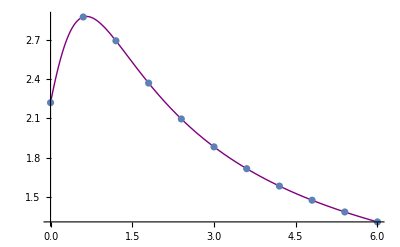

```mathematica
graph2Npn=Plot[NPn2[x],{x,a,b}]
Show[graphic,graph2,graph2Npn]
```

```mathematica
Print["Ln1[x0]=",Ln1[x0],", Ln2[x0]=",Ln2[x0]]
```

Ln1[x0]=2.07807, Ln2[x0]=2.08365

```mathematica
Print["Pn1[x0]=",Pn1[x0],", Pn2[x0]=",Pn2[x0]]
```

Pn1[x0]=2.07807, Pn2[x0]=2.08365

```mathematica
Print["Npn1[x0]=",NPn1[x0],", Npn2[x0]=",Npn2[x0]]
```

Npn1[x0]=2.07807, Npn2[x0]=2.08365

```mathematica
Rn1[x_]=Abs[f[x]-NPn1[x]]
graphErr1=Plot[Rn1[x],{x,a,b},PlotRange->Full]
```

Abs[-2.22144-2.25583 x+2.63235 x^2-1.19771 x^3+0.278813 x^4-0.0326847 x^5+0.0015262 x^6+(π+3 x)/(√(1+x^2+√((1+x^2)^3)))]

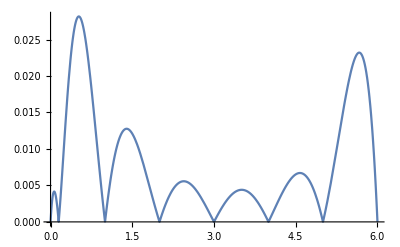

```mathematica
maxErr1=FindMaximum[Rn1[x],{x,a,b}]
```

{0.0281655,{x→0.519073}}

Abs[-2.22144-2.49199 x+3.06027 x^2-1.2842 x^3-0.00622875 x^4+0.240723 x^5-0.114705 x^6+0.0277141 x^7-0.00384248 x^8+0.000291019 x^9-9.36214×10^-6 x^10+(π+3 x)/(√(1+x^2+√((1+x^2)^3)))]

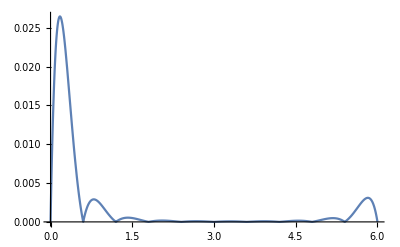

```mathematica
Rn2[x_]=Abs[f[x]-Npn2[x]]
graphErr2=Plot[Rn2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErr2=FindMaximum[Rn2[x],{x,5.5,b}]
```

{0.00309916,{x→5.82378}}

```mathematica
FindMaximum[Rn2[x],{x,5.5,b}]
```

```mathematica
{0.003099155173753587,{x->5.8237843884895355}}
```